```mathematica
(*Load the finite element package*)Needs["NDSolve`FEM`"];

(*Define parameters*)
omega=1;    (*Replace with your desired value*)
r=1;        (*Replace with your desired value*)
xMax=12;    (*Set the maximum x value*)
zMax=22;    (*Set the maximum z value*)
LD=1/omega;

(*Define the computational domain*)
region=Rectangle[{-xMax,0},{xMax,zMax}];

(*Define the PDE with NeumannValue terms included*)
pde=-Laplacian[C[x,z],{x,z}]+NeumannValue[omega*C[x,z]-r*UnitStep[-x],z==0]+NeumannValue[0,x==-xMax||x==xMax||z==zMax]==0;

(*Increase spatial resolution by refining the mesh*)
meshOptions={"MaxCellMeasure"->0.001};  (*Further decrease for finer mesh*)

(*Define the Analytical Solutions*)
CAnalytical[x_]:=Module[{nMax=50,sum=0},sum=Sum[Module[{kn=Pi (2 n+1)/(2 xMax)},(Sin[kn x] Cosh[kn zMax])/(kn (kn Sinh[kn zMax]+omega Cosh[kn zMax]))],{n,0,nMax}];
(r/(2 omega))-(r/xMax) sum];

CAnalyticApprox[x_]:=(r/omega)*(HeavisideTheta[-x]+(Cos[x/LD]/π) Sign[x] (π/2-SinIntegral[Abs[x]/LD])+(Sin[x/LD]/π) CosIntegral[Abs[x]/LD]);

CAnalyticlFF[x_]:=(r/omega)*(HeavisideTheta[-x]+LD/(π x));

CAnalyticlNF[x_]:=(r/(π omega))*(HeavisideTheta[-x]+Sign[x] (π/2-(x/LD))+(x/LD) (Log[Abs[x]/LD]+EulerGamma));
```

```mathematica
(*Generate x-values*)
xList=DeleteDuplicates[Subdivide[-xMax,xMax,70],Abs[#1-#2]<10^-6&];
xList=Select[xList,Abs[#]>10^-6&];  (*Exclude x=0 to avoid division by zero*)
```

```mathematica
(*Compute solution values*)
solutionList=Reap[Do[Quiet[Check[With[{y=solution[x-0.005,0]},If[NumericQ[y],Sow[{x,y}]]],Null]],{x,xList}]][[2,1]];

(*Compute CAnalytical values*)
CAnalyticalList=Reap[Do[Quiet[Check[With[{y=CAnalytical[x+0.005]},If[NumericQ[y],Sow[{x,y}]]],Null]],{x,xList}]][[2,1]];

(*Compute CAnalyticApprox values*)
CAnalyticApproxList=Reap[Do[Quiet[Check[With[{y=CAnalyticApprox[x]},If[NumericQ[y],Sow[{x,y}]]],Null]],{x,xList}]][[2,1]];

(*x-values for CAnalyticlFF*)
xListFF=Select[xList,#>=7&];

(*Compute CAnalyticlFF values*)
CAnalyticlFFList=Reap[Do[Quiet[Check[With[{y=CAnalyticlFF[x]+0.005},If[NumericQ[y],Sow[{x,y}]]],Null]],{x,xListFF}]][[2,1]];

(*x-values for CAnalyticlNF*)
xListNF=Select[xList,0.0001<=#<=0.35&];

(*Compute CAnalyticlNF values*)
CAnalyticlNFList=Reap[Do[Quiet[Check[With[{y=CAnalyticlNF[x]-0.005},If[NumericQ[y],Sow[{x,y}]]],Null]],{x,xListNF}]][[2,1]];

(*Combine datasets*)
datasets={solutionList,CAnalyticalList,CAnalyticApproxList,CAnalyticlFFList,CAnalyticlNFList};
```

```mathematica
(*Solve the PDE*)
solution=NDSolveValue[pde,C,{x,z}∈region,Method->{"FiniteElement","MeshOptions"->meshOptions}];
```

```mathematica
plot1D=ListPlot[datasets,Joined->False,(*No lines connecting the markers*)PlotRange->All,FrameLabel->{Style["x",FontFamily->"Helvetica Neue",FontSize->22,FontColor->Black],Style["C(x,0)",FontFamily->"Helvetica Neue",FontSize->22,FontColor->Black]},PlotStyle->{{Black},(*Numerical:Black*){Red},(*Analytical:Red*){Blue},(*Approx.Analytical:Blue*){Purple},(*CAnalyticlFF:Purple*){Green}  (*CAnalyticlNF:Green*)},
PlotMarkers->{
{Graphics[{EdgeForm[{Black,AbsoluteThickness[2]}],Disk[]}],14},(*Hollow Circle*)
{Graphics[{EdgeForm[{Red,AbsoluteThickness[2]}],FaceForm[None],Rectangle[]}],14},(*Hollow Square*)
{Graphics[{EdgeForm[{Blue,AbsoluteThickness[2]}],FaceForm[None],Triangle[]}],14},(*Hollow Triangle*){Graphics[{EdgeForm[{Orange,AbsoluteThickness[2]}],FaceForm[None],Disk[]}],14},(*Hollow Pentagon*){Graphics[{EdgeForm[{Green,AbsoluteThickness[2]}],FaceForm[None],Disk[]}],14}   (*Hollow Hexagon*)},
PlotLegends->Placed[PointLegend[
{Graphics[{EdgeForm[{Black,AbsoluteThickness[2]}],FaceForm[None],Disk[]}],Graphics[{EdgeForm[{Red,AbsoluteThickness[2]}],FaceForm[None],Rectangle[]}],Graphics[{EdgeForm[{Blue,AbsoluteThickness[2]}],FaceForm[None],Triangle[]}],Graphics[{EdgeForm[{Purple,AbsoluteThickness[2]}],FaceForm[None],RegularPolygon[5]}],Graphics[{EdgeForm[{Green,AbsoluteThickness[2]}],FaceForm[None],RegularPolygon[6]}]},{"Numerical Solution","Eq. S11","Eq. S12","Eq. S13","Eq. S14"},LabelStyle->{FontFamily->"Helvetica Neue",FontSize->14},LegendMarkerSize->{40,15}],{0.8,0.85}],GridLines->Automatic,ImageSize->800,BaseStyle->{FontFamily->"Helvetica Neue",FontSize->14},Frame->True,FrameStyle->Directive[GrayLevel[0],13,FontFamily->"Helvetica Neue",AbsoluteThickness[1.0]],FrameTicks->Automatic];
```

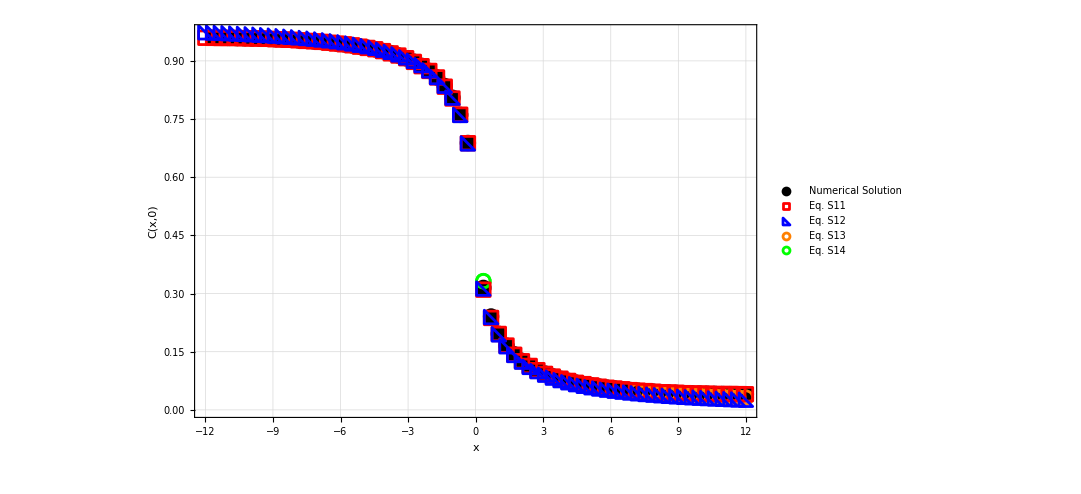

```mathematica
(*Display the plot*)
plot1D
```